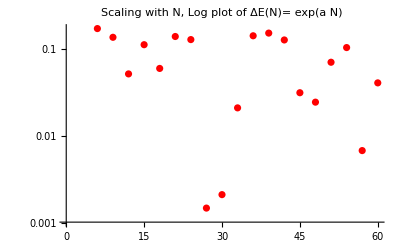

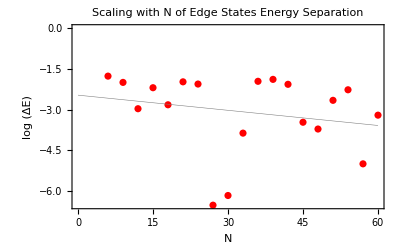

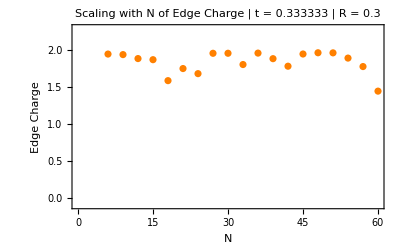

```mathematica
Begin["Pr1`"];
ClearAll["Pr1`*"];
Clear[v1, w1, v2, w2, R, W, Ncells];

v1=2/3;
w1=1; (* Measure energy in units of w *)
v2 = 1/3;
w2 = v2;
RValues={0.3}; (* List of n.n. disorder strengths *)
WValues={0}; (* List of n.n.n. disorder strengths *)

NcellsValues=Table[3i , {i,2,20}]; (* List of numbers of unift cells *) (* Table[3i , {i,2,20}] *)
dEnedgeValues= Table[0 ,{i,1,Length[NcellsValues]}];  (* List of energy differences between edge states *)
LeftChargeValues= Table[0 ,{i,1,Length[NcellsValues]}];  (* List of left edge charge values *)
RightChargeValues= Table[0 ,{i,1,Length[NcellsValues]}];  (* List of left edge charge values *)

PBC=False; (* PBC or OBC? *)
plotBands=False; (* Display plots of energy bands? *)
plotEdge=False; (* Display plots of edge states? *)
plotLinComb=False; (* Display plots of linear combinations of edge states? *)

(* Cycle on unit cells number *)
For[
k=1,k≤ Length[NcellsValues],k++,

(* Cycle on n.n. disorder strength R *)
For[
m=1,m≤Length[RValues],m++,

(* Cycle on n.n.n. disorder strength W *)
For[
l=1,l≤Length[WValues],l++,

Ncells=NcellsValues[[k]];
(*Print["\n\nNcells = ", Ncells,"\n\n"];*)

R=RValues[[m]];
(*Print["\nR = ", R,"\n"];*)

W=WValues[[l]];
(*Print["\nW = ", W,"\n"];*)

(* TB Hamiltonian Matrix *)
Hmatrix  = SparseArray[
{
{i_,j_}/;Abs[i-j]==1&&If[i>j,Mod[i,2]==1,Mod[j,2]==1]->w1,
{i_,j_}/;Abs[i-j]==1&&If[i>j,Mod[i,2]==0,Mod[j,2]==0]->v1,
{i_,j_}/;Abs[i-j]==2&&If[i>j,Mod[i,2]==1,Mod[j,2]==1]-> v2,
{i_,j_}/;Abs[i-j]==2&&If[i>j,Mod[i,2]==0,Mod[j,2]==0]->w2
}
,{2*Ncells,2*Ncells},0];
Hmatrix = Normal[Hmatrix]; (* Reverting to dense matrix [fast diagonalization purposes, for big Ncells] *)

(* Add PBC if present, with disorder already included *)
If[PBC,
Hmatrix[[1,2*Ncells]]=Hmatrix[[2*Ncells,1]]=w1+RandomReal[{-R,R}];
Hmatrix[[1,2*Ncells-1]]=Hmatrix[[2*Ncells-1,1]]=v2+RandomReal[{-W,W}];
Hmatrix[[2,2*Ncells]]=Hmatrix[[2*Ncells,2]]=w2+RandomReal[{-W,W}];
];
(*MatrixForm[Hmatrix]*)

(* Disorder on n.n. hoppings *)
For[i=1, i<2*Ncells, i++, r=RandomReal[{-R,R}]; 
Hmatrix[[i,i+1]]=Hmatrix[[i,i+1]]+r;  
Hmatrix[[i+1,i]]=Hmatrix[[i+1,i]]+r;  
];
(*MatrixForm[Hmatrix]*)

(* Disorder on n.n.n. hoppings *)
For[i=1, i<2*Ncells-1, i++, r=RandomReal[{-W,W}]; 
Hmatrix[[i,i+2]]=Hmatrix[[i,i+2]]+r;  
Hmatrix[[i+2,i]]=Hmatrix[[i+2,i]]+r;  
];
(*MatrixForm[Hmatrix]*)


(* Eigenthings *)
{En,Cn} = Transpose[Sort[Transpose[Eigensystem[Hmatrix]],#1[[1]]<#2[[1]]&]];

(* Energy Levels *)
plotEn[i_,x_]:=En[[i]];
If[plotBands,
Print[Show[Table[Plot[plotEn[i,x], {x,0, 0.5}, PlotRange-> {Min[En]-0.3,Max[En]+0.3},Axes->{False, True},PlotStyle -> {Black,Thickness[0.001], Opacity[0.3]}, Frame -> True, FrameTicks -> {None,Automatic}, FrameLabel -> {,"Energy [units of w]"},PlotLabel ->StringTemplate["SSH OBC Levels for v = `1`, w = `2`"][v1,w1]], {i,1,2*Ncells}]]];
];

(* Edge States *)
edge1=Chop[Cn[[Ncells]]];   (* We have sorted eigenvalues *)			
edge2=Chop[Cn[[Ncells+1]]];           
Enedge1 = En[[Ncells]];
Enedge2 = En[[Ncells +1]];
dEnedge = Abs[Enedge1 - Enedge2];
(*Print["\n\nEnedge1 = ",Enedge1, "\n","Enedge2 = ",Enedge2, "\n","dEnedge = ",dEnedge, "\n"];*)

dEnedgeValues[[k]]=dEnedge;

(* Edge states *)
wfedge1[x_]:=Sum[edge1[[n]]*Exp[-Abs[3*(x-n)]],{n,1,2*Ncells}];
wfedge2[x_]:=Sum[edge2[[n]]*Exp[-Abs[3*(x-n)]],{n,1,2*Ncells}];

edgeWeight1 = Max[Sum[(edge1[[n]])^2,{n,2*Ncells-10,2*Ncells}],Sum[(edge1[[n]])^2,{n,1,10}]]/Sum[(edge1[[n]])^2,{n,1,2*Ncells}];
(*Print["\n\nedgeWeight1 = ",edgeWeight1];*)

edgeWeight2 = Max[Sum[(edge2[[n]])^2,{n,2*Ncells-10,2*Ncells}],Sum[(edge2[[n]])^2,{n,1,10}]]/Sum[(edge2[[n]])^2,{n,1,2*Ncells}];
(*Print["\n\nedgeWeight2 = ",edgeWeight2];*)

If[plotEdge,
Print["\n\nEdge states\n"];
Print[Plot[{wfedge1[x],wfedge2[x]},{x,0, 1/4*Ncells},PlotRange -> {-1,1}, Filling -> Axis, Frame -> True,FrameLabel -> {x,ψ[x]}, PlotLabel -> StringTemplate["Edge States Amplitude for v = `1`, w = `2`"][v1,w1]]]
Print[Plot[{wfedge1[x],wfedge2[x]},{x,7/4*Ncells, 2*Ncells+1},PlotRange -> {-1,1}, Filling -> Axis, Frame -> True, FrameLabel -> {x,ψ[x]}, PlotLabel -> StringTemplate["Edge States Amplitude for v = `1`, w = `2`"][v1,w1]]
]];

(* Linear combinations of edge states *)
linComb1[x_]:=Sum[1/Sqrt[2](edge1[[n]]+edge2[[n]])*Exp[-Abs[3*(x-n)]],{n,1,2*Ncells}];
linComb2[x_]:=Sum[1/Sqrt[2](edge1[[n]]-edge2[[n]])*Exp[-Abs[3*(x-n)]],{n,1,2*Ncells}];

edgeCombWeight1 = Max[Sum[(edge1[[n]]+edge2[[n]])^2,{n,2*Ncells-10,2*Ncells}],Sum[(edge1[[n]]+edge2[[n]])^2,{n,1,10}]]/Sum[(edge1[[n]]+edge2[[n]])^2,{n,1,2*Ncells}];
(*Print["\n\nedgeCombWeight1 = ",edgeCombWeight1];*)

edgeCombWeight2 = Max[Sum[(edge1[[n]]-edge2[[n]])^2,{n,2*Ncells-10,2*Ncells}],Sum[(edge1[[n]]-edge2[[n]])^2,{n,1,10}]]/Sum[(edge1[[n]]-edge2[[n]])^2,{n,1,2*Ncells}];
(*Print["\n\nedgeCombWeight2 = ",edgeCombWeight2];*)

If[plotLinComb,
Print["\n\nLinear combinations of edge states\n"];
Print[Plot[{linComb1[x],linComb2[x]},{x,0, 1/4*Ncells},PlotRange -> {-1,1}, Filling -> Axis, Frame -> True,FrameLabel -> {x,ψ[x]}, PlotLabel -> StringTemplate["Edge States Amplitude for v = `1`, w = `2`"][v1,w1]]]
Print [Plot[{linComb1[x],linComb2[x]},{x,7/4*Ncells, 2*Ncells+1},PlotRange -> {-1,1}, Filling -> Axis, Frame -> True,FrameLabel -> {x,ψ[x]},PlotLabel -> StringTemplate["Edge States Amplitude for v = `1`, w = `2`"][v1,w1]]
]];

LeftCharge = Max[edgeWeight1,edgeCombWeight1];
(*Print["\n\nLeftCharge = ",LeftCharge]*);
LeftChargeValues[[k]] = LeftCharge;
(*Print["\n\nLeftChargeValues = ",LeftChargeValues]*);
RightCharge =  Max[edgeWeight2,edgeCombWeight2];
(*Print["\n\nRightCharge = ",RightCharge]*);
RightChargeValues[[k]] = RightCharge;
(*Print["\n\nLeftChargeValues = ",RightChargeValues]*);

](* Cycle on W values CLOSING *)

] (* Cycle on R values CLOSING *)

] (* Cycle on unit cells number CLOSING*)


If[Length[NcellsValues]>1,

Print["\n\n"];
(* Scaling of energy difference with N, we expect exponential decay *)
data=Table[{NcellsValues[[i]],dEnedgeValues[[i]]},{i,1,Length[NcellsValues]}];
Print[ListLogPlot[ data,PlotLabel->"Scaling with N, Log plot of ΔE(N)= exp(a N)", AxesStyle->Gray,PlotStyle->{Red}]];

dataLog=Table[{NcellsValues[[i]],Log[dEnedgeValues[[i]]]},{i,1,Length[NcellsValues]}];
Print["\n"]; 
(*  Linear fit: find a<0, where ΔE(N)=exp(a N) *)
line[x_]=Fit[dataLog, {1,x},x];
Print[Show[
ListPlot[ dataLog,PlotLabel->"Scaling with N of Edge States Energy Separation", Frame->True,FrameLabel -> {"N","log (ΔE)"},PlotStyle->{Red}],Plot[line[x],{x,0,NcellsValues[[Length[NcellsValues]]]}, PlotStyle -> {Gray, Thickness[0.001]}]]];

(* Scaling of Left Edge Charge with N, we expect it to be constant *)
dataLeft=Table[{NcellsValues[[i]],LeftChargeValues[[i]]},{i,1,Length[NcellsValues]}];
(*Print["\n\ndataLeft = ",dataLeft];*)
dataRight=Table[{NcellsValues[[i]]*0,RightChargeValues[[i]]},{i,1,Length[NcellsValues]}];
 (*Print["\n\ndataRight = ",dataRight];*)
dataEdge = dataLeft + dataRight;
(*Print["\n\ndataEdge = ",dataEdge];*)
 Print[ListPlot[ dataEdge,PlotRange -> {-0.1, 2.3},PlotLabel->StringTemplate["Scaling with N of Edge Charge | t = `1` | R = `2`"][v2,R], Frame -> True,FrameLabel -> {"N","Edge Charge"}, PlotStyle -> Orange]];
]

End[];
```

```mathematica
(* Space for trials *)

Begin["Pr1`"];
En;

Array[#&,6,{0.05,0.15}]

1/0.40534543029193115
End[]
```

{0.05,0.07,0.09,0.11,0.13,0.15}

2.46703

Pr1`

```mathematica
"Pr1`"
```

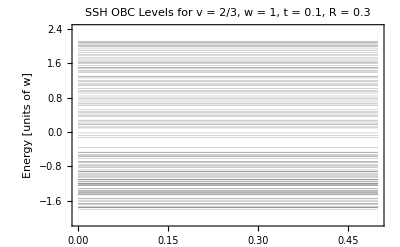

```mathematica
(* Plotting Energy Levels *)
Print[Show[Table[Plot[plotEn[i,x], {x,0, 0.5}, PlotRange-> {Min[En]-0.3,Max[En]+0.3},Axes->{False, True},PlotStyle -> {Black,Thickness[0.001], Opacity[0.3]}, Frame -> True, FrameTicks -> {None,Automatic}, FrameLabel -> {,"Energy [units of w]"},PlotLabel ->StringTemplate["SSH OBC Levels for v = 2/3, w = `2`, t = `3`, R = `4`"][v1,w1,v2, R]], {i,1,2*Ncells}]]];
```

Edge states

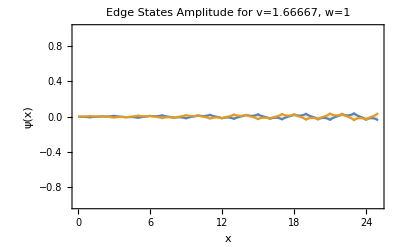

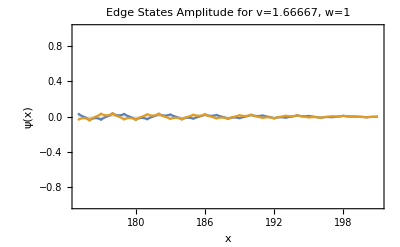

Edge state 1

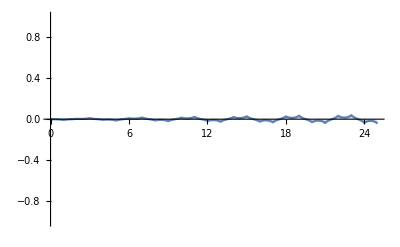

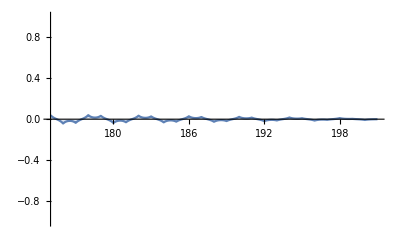

Edge state 2

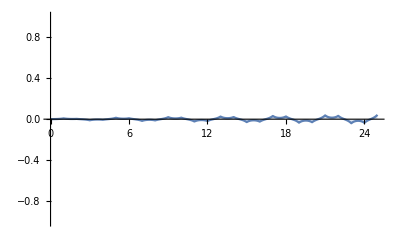

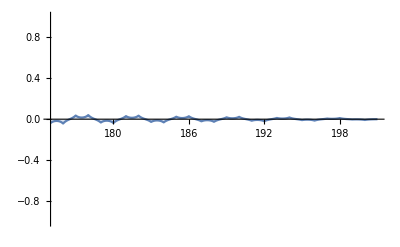

Linear combinations of edge states

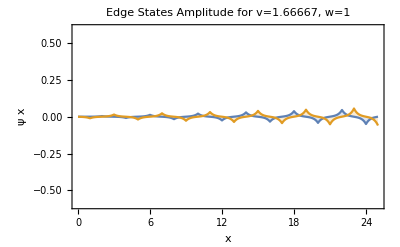

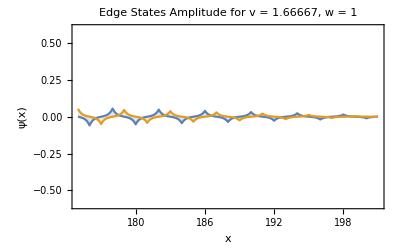

Lin comb 1

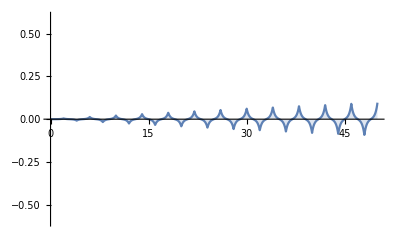

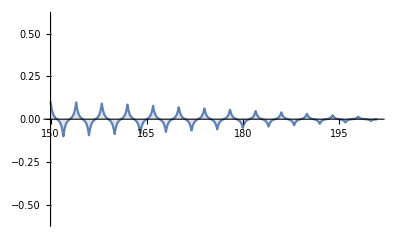

Lin comb 2

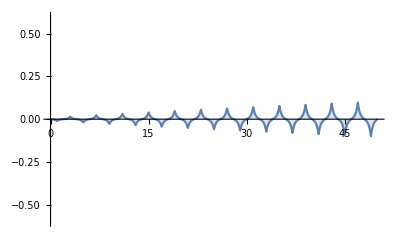

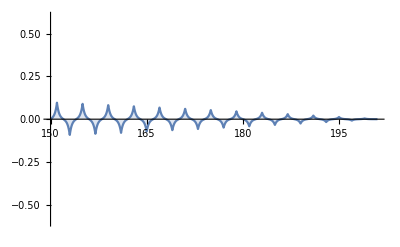

Pr1`

```mathematica
Begin["Pr1`"];

(* Plot of the two edge states - or the two linear combinations - together *)

(* Edge states *)
Print["\n\nEdge states\n"];
wfedge1[x_]:=Sum[edge1[[n]]*Exp[-Abs[3*(x-n)]],{n,1,2*Ncells}];
wfedge2[x_]:=Sum[edge2[[n]]*Exp[-Abs[3*(x-n)]],{n,1,2*Ncells}];
Plot[wfedge1[x],{x,0, Ncells},PlotRange -> {-1,1}, Filling -> Axis, Frame -> True,FrameLabel -> {x,ψ[x]}, PlotLabel -> StringTemplate["Edge States Amplitude for v=`1`, w=`2`"][v1,w1]]
Plot[{wfedge1[x],wfedge2[x]},{x,7/4*Ncells, 2*Ncells+1},PlotRange -> {-1,1}, Filling -> Axis, Frame -> True, FrameLabel -> {x,ψ[x]}, PlotLabel -> StringTemplate["Edge States Amplitude for v=`1`, w=`2`"][v1,w1]]

Print["\n\nEdge state 1\n"];
Print[Plot[wfedge1[x],{x,0, 1/4*Ncells},PlotRange -> {-1,1}, Filling -> Axis]];
Print[Plot[wfedge1[x],{x,7/4*Ncells, 2*Ncells+1},PlotRange -> {-1,1}, Filling -> Axis]];

Print["\n\nEdge state 2\n"];
Print[Plot[wfedge2[x],{x,0, 1/4*Ncells},PlotRange -> {-1,1}, Filling -> Axis]];
Print[Plot[wfedge2[x],{x,7/4*Ncells, 2*Ncells+1},PlotRange -> {-1,1}, Filling -> Axis]];

(* Linear combinations of edge states *)
Print["\n\nLinear combinations of edge states\n"];
linComb1[x_]:=Sum[1/Sqrt[2](edge1[[n]]+edge2[[n]])*Exp[-Abs[3*(x-n)]],{n,1,2*Ncells}];
linComb2[x_]:=Sum[1/Sqrt[2](edge1[[n]]-edge2[[n]])*Exp[-Abs[3*(x-n)]],{n,1,2*Ncells}];
Plot[{linComb1[x],linComb2[x]},{x,0, 1/4*Ncells},PlotRange -> {-.6,.6}, Filling -> Axis, Frame -> True,FrameLabel -> {x,ψ(x)}, PlotLabel -> StringTemplate["Edge States Amplitude for v=`1`, w=`2`"][v1,w1]]
Plot[{linComb1[x],linComb2[x]},{x,7/4*Ncells, 2*Ncells+1},PlotRange -> {-.6,.6}, Filling -> Axis, Frame -> True,FrameLabel -> {x,ψ[x]},PlotLabel -> StringTemplate["Edge States Amplitude for v = `1`, w = `2`"][v1,w1]]

Print["\n\nLin comb 1\n"];
Print[Plot[linComb1[x],{x,0, 1/2*Ncells},PlotRange -> {-.6,.6}, Filling -> Axis]];
Print[Plot[linComb1[x],{x,6/4*Ncells, 2*Ncells+1},PlotRange -> {-.6,.6}, Filling -> Axis]];

Print["\n\nLin comb 2\n"];
Print[Plot[linComb2[x],{x,0, 1/2*Ncells},PlotRange -> {-.6,.6}, Filling -> Axis]];
Print[Plot[linComb2[x],{x,6/4*Ncells, 2*Ncells+1},PlotRange -> {-.6,.6}, Filling -> Axis]];

End[]
```

(*Notation, OBC*)

(0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0)

(*Notation, PBC*)

(0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1
v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2
v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1 | v2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0 | w1 | w2
v2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v2 | w1 | 0 | v1
w1 | w2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | w2 | v1 | 0)

(*Perfect Choice of Parameters*)

v1=2/3;
w1=1; (* Measure energy in units of w *)
v2 = 0;
w2 = 0;
R=0; (* n.n. disorder strength *)
W=0; (* n.n.n. disorder strength *)

PBC=False; (* PBC or OBC? *)